```mathematica
(**Programming Lanauge: Wolfram Language (Mathematica)**)

(**Problem 2**)

(**Mathematica is weird with how it handles variables so people often include this to amke it less annoying**)
Remove["Global`*"]

f[x_]:=x^2-4x+3

p0 = 1.99;
p1 =p0;
tol = 10^-5;
k= 0;

While[

p0 = p1;
p1 = p0 - f[p0]/f'[p0];
Abs[p1-p0]>=tol,

k= k+1;

Print[Subscript["p", k]," = ",N[p1,10]]
]
```

p_1 = -48.005

p_2 = -23.0125

p_3 = -10.5262

p_4 = -4.30304

p_5 = -1.23084

p_6 = 0.229819

p_7 = 0.832453

p_8 = 0.987978

p_9 = 0.999929

p_10 = 1.

```mathematica
p0 = 2.01;
p1 =p0;
tol = 10^-5;
k= 0;

While[

p0 = p1;
p1 = p0 - f[p0]/f'[p0];
Abs[p1-p0]>=tol,

k= k+1;

Print[Subscript["p", k]," = ",N[p1,10]]
]
```

p_1 = 52.005

p_2 = 27.0125

p_3 = 14.5262

p_4 = 8.30304

p_5 = 5.23084

p_6 = 3.77018

p_7 = 3.16755

p_8 = 3.01202

p_9 = 3.00007

p_10 = 3.

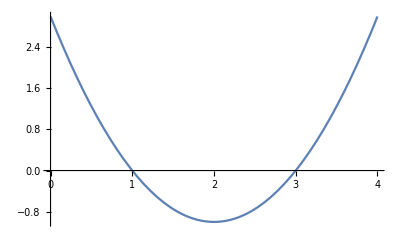

{{x→2}}

```mathematica
(**What we find is that this time even though 2.01 is close to 1.99 the sequence converges to the other root of 3.**)

Plot[f[x],{x,0,4}]
Solve[f'[x]==0,x]

(**This is because (as shown with the above code) the sign of the derivative of f[x] changes at x = 2.**)
```

```mathematica
(**Problem 3**)

Remove["Global`*"]

(**In Mathematica all reserved names begin with capital letters, even the constant e!**)
g[x_]:=3x-E^x

p0=1;
p1 = 2;

tol = 10^-5;

p2 = p1;
p1 = p0;

k = 0;

While[
p0 = p1;
p1 = p2;

p2 = p1 - (g[p1](p1-p0))/(g[p1]-g[p0]);

Abs[p2-p1]>=tol|| k > 3,

k=k+1;
Print[Subscript["p", k]," = ",N[p2,10]]
]

(**In this case the sequence does not converge.**)
```

p_1 = 1.16861534

p_2 = 1.311516555

p_3 = 1.79704301

p_4 = 1.436777893

p_5 = 1.486766287

p_6 = 1.515325761

p_7 = 1.512011934

```mathematica
g[x_]:=3x-E^x

(**Mathematica's answer to this problem to this problem to see if we are right**)
NSolve[g[x]==0,x]

(**We choose this points because we know the root is somewhere near 1.5**)
p0=2;
p1 = 1.5;

tol = 10^-5;

p2 = p1;
p1 = p0;

k = 0;

While[
p0 = p1;
p1 = p2;

p2 = p1 - (g[p1](p1-p0))/(g[p1]-g[p0]);

Abs[p2-p1]>=tol,

k=k+1;
Print[Subscript["p", k]," = ",N[p2,10]]
]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.619061},{x→1.51213}}

p_1 = 1.50651

p_2 = 1.51224

p_3 = 1.51213